```mathematica
MyLorentzian[x_,xc_,a_]:=1/(1+((x-xc)/a)^2)
```

```mathematica
a = 0.1;
```

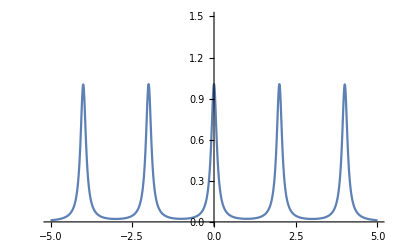

```mathematica
plot = Plot[MyLorentzian[x,0,a] + MyLorentzian[x,2,a] + MyLorentzian[x,4,a] +MyLorentzian[x,-2,a] +MyLorentzian[x,-4,a]//Evaluate,{x,-5,5}, PlotRange->{{-5, 5},{0, 1.5}}]
```

```mathematica
Export[NotebookDirectory[]<>"5 lorentzians.pdf",plot]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\5 lorentzians.pdf

## Single ring

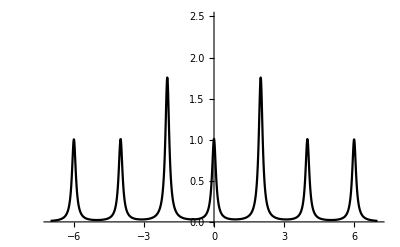

```mathematica
plot = Plot[MyLorentzian[x,0,a] + 1.75*MyLorentzian[x,2,a] + MyLorentzian[x,4,a] + + MyLorentzian[x,6,a] +1.75*MyLorentzian[x,-2,a] +MyLorentzian[x,-4,a]+ + MyLorentzian[x,-6,a]//Evaluate,{x,-7,7}, PlotStyle->{Black}, PlotRange->{{-7, 7},{0, 2.5}}]
```

```mathematica
Export[NotebookDirectory[]<>"SingleRingMathematica.pdf",plot]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\Mathematica\SingleRingMathematica.pdf

## Photonic Molecule

```mathematica
MainTriplet[x_]:= MyLorentzian[x,0,a] + 1.75*MyLorentzian[x,1,a] + 1.75*MyLorentzian[x,-1,a]
```

```mathematica
Adjacent[x_, delta_]:= MyLorentzian[x,4.5-delta,a] + MyLorentzian[x,5.5-delta,a] + MyLorentzian[x,3.5-delta,a] +  MyLorentzian[x,-4.5-delta,a] + MyLorentzian[x,-5.5-delta,a] + MyLorentzian[x,-3.5-delta,a]
```

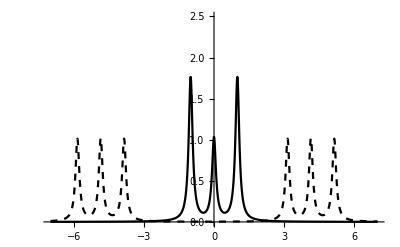

```mathematica
plot = Plot[{MainTriplet[x], Adjacent[x,0.35]}//Evaluate,{x,-7,7}, PlotStyle->{Black, {Dashed,  Black}}, PlotRange->{{-7, 7},{0, 2.5}}]
```

```mathematica
Export[NotebookDirectory[]<>"PhotonicMoleculeMathematica.pdf",plot]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\Papers\Journals\2024 - Nathalia - DOPO in photonic molecules\Figures\Mathematica\PhotonicMoleculeMathematica.pdf

## New

#### Single ring new

```mathematica
Spectrum[x_, xc_, a_,N_, D1_,D2_]:=Sum[If[Abs[μ]==1,1.75,1]×MyLorentzian[x, xc+μ*D1+D2*μ^2/2, a],{μ,-(N-1)/2,(N-1)/2}]
```

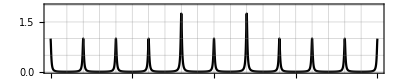

```mathematica
plot = Plot[Spectrum[x, 0, .045,11, 2,-.0]//Evaluate,{x,-10,10}, PlotStyle->{Black}, PlotRange->{{-10, 10},{0, 2.}}, AspectRatio->.2,GridLines->{Table[i, {i,-9,9,1}],Table[i, {i,0,2,.5}]}, Frame-> True]
```

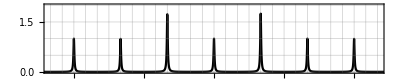

```mathematica
plot = Plot[Spectrum[x, 0, .045,11, 4,-.0]//Evaluate,{x,-15,15}, PlotStyle->{Black}, PlotRange->{{-14, 14},{0, 2.}}, AspectRatio->.2,GridLines->{Table[i, {i,-14,14,1}],Table[i, {i,0,2,.5}]}, Frame-> True]
```

```mathematica
(*Export[NotebookDirectory[]<>"SingleRingMathematica.pdf",plot]*)
```

#### Photonic Molecule new

```mathematica
Triplet[x_, xc_, a_, J1_,Assymetry_, μ_]:=MyLorentzian[x,xc,a] + If[μ==0,Assymetry,1]*MyLorentzian[x,xc+J1,a] + If[μ==0,Assymetry,1]*MyLorentzian[x,xc-J1,a]
Spectrum[x_, xc_, a_, J1_,Assymetry_,N_, D1_,D2_]:=Sum[Triplet[x, xc+μ*D1+D2*μ^2/2, a, J1,Assymetry, μ],{μ,-(N-1)/2,(N-1)/2}]
```

```mathematica
(*plot = Plot[Spectrum[x, 0, 0.015, .2,1.75,7,1.85,-.12]//Evaluate,{x,-9,9}, PlotStyle->{Black}, PlotRange->{{-7, 7},{0, 2.}}, AspectRatio->.2, GridLines->{Table[i, {i,-7,7,1}],Table[i, {i,0,2,.5}]}, Frame-> True] *)
```

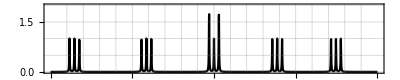

```mathematica
plot = Plot[Spectrum[x, 0, 0.015, .3,1.75,5,4,-.27]//Evaluate,{x,-10,10}, PlotStyle->{Black}, PlotRange->{{-10,10},{0, 2.}}, AspectRatio->.2, GridLines->{Table[i, {i,-9,9,1}],Table[i, {i,0,2,.5}]}, Frame-> True]
```

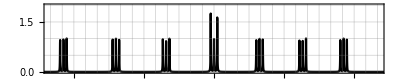

```mathematica
plot = Plot[Spectrum[x, 0, 0.015, .28,1.75,7,4,-.2]//Evaluate,{x,-15,15}, PlotStyle->{Black}, PlotRange->{{-14,14},{0, 2.}}, AspectRatio->.2, GridLines->{Table[i, {i,-14,14,1}],Table[i, {i,0,2,.5}]}, Frame-> True]
```